```mathematica
Clear[x]
```

```mathematica
f[x_]:=x^2
```



```mathematica
Plot[f[x],{x,-2,2}]
```

```mathematica
f[a]
```

a^2

```mathematica
Solve[D[f[x],x]==0]
```

{{x→0}}

```mathematica
Clear[f]
f[x_]:=2x
```

```mathematica
D[f[x],x]==0
```

False

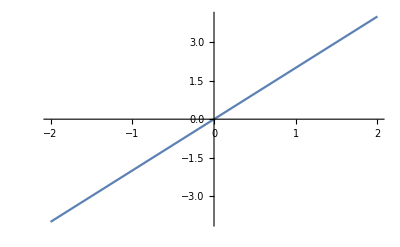

```mathematica
Plot[f[x],{x,-2,2}]
```

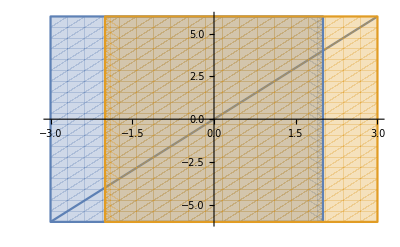

```mathematica
Show[Plot[f[x],{x,-3,3}],RegionPlot[{x≤2,x≥-2},{x,-3,3},{y,-6,6}],PlotRange->All]
```

```mathematica
Clear[f]
f[x_,y_]:=2x+y
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Clear[f]
f[x_,y_]:=2x^2+y^2
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Solve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0,y→0}}

```mathematica
Clear[f]
f[x_,y_]:=Sin[y]*Sin[x]+0.1x^2+0.1y^2
Plot3D[f[x,y],{x,-4,4},{y,-4,4}]
```

-Graphics3D-

```mathematica
NSolve[{D[f[x,y],x]==0,D[f[x,y],y]==0},{x,y}]
```

{{x→0.,y→0.}}

```mathematica
Clear[f]
f[x_,y_]:=2x*y
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Rastrigin function
```

```mathematica
Clear[f]
A=10
n=2
f[x_,y_]:=A*n + (x^2-10*Cos[2*π*x])+ (y^2-10*Cos[2*π*y])
```

10

2

```mathematica
D[f[x,y],x]
```

2 x+20 π Sin[2 π x]

```mathematica
D[f[x,y],y]
```

2 y+20 π Sin[2 π y]

```mathematica
Plot3D[f[x,y],{x,-5.12,5.12},{y,-5.12,5.12}]
```

-Graphics3D-